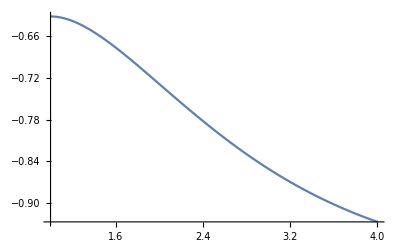

With integration by parts, the integral evaluates to -2.35582

```mathematica
(* Michael Barile 
MATH 68500
November 13, 2017 *)

(* 5.1 *)

(* Problem 1a *)

f[x_]:=x*Exp[-x]-1;
Plot[f[x],{x,1,4}]

(* Integration by parts *)

ansnum =N[(-4*Exp[-4]-Exp[-4]-4)-(-1*Exp[-1]-Exp[-1]-1),6];
Print["With integration by parts, the integral evaluates to ",ansnum]
```

```mathematica
(* Problem 1b *)
```

```mathematica
ansmath=N[Integrate[f[x],{x,1,4}],6];
Print["With the built-in integration function, the integral evaluates to ",ansmath,", so both methods produce essentially the same result."];
```

With the built-in integration function, the integral evaluates to -2.35582, so both methods produce essentially the same result.

```mathematica
(* Problem 2a *)

(* Trapezoid Method *)

deltax=.5;
x0=1;
xvec={};
While[Max[xvec]<4,
AppendTo[xvec,x0];
x0=x0+deltax
];

vals={};

For[i=1,i≤Length[xvec]-1,++i,
AppendTo[vals,(f[xvec[[i+1]]]+f[xvec[[i]]])*(xvec[[i+1]]-xvec[[i]])/2]
];
calc=Total[vals];
Print["With the trapezoid method, the integral evaluates to ", calc];
```

With the trapezoid method, the integral evaluates to -2.3569

```mathematica
(* Problem 2b *)

(* Simpson's Rule *)

valssimp={};
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[valssimp,(1/6*f[xvec[[i+1]]]+2/3*f[(xvec[[i+1]]+xvec[[i]])/2]+1/6*f[xvec[[i]]])*(xvec[[i+1]]-xvec[[i]])]
];
calcsimp=Total[valssimp];
Print["With Simpson's rule, the integral evaluates to ",calcsimp];
```

With Simpson's rule, the integral evaluates to -2.35584

```mathematica
(* If we take the answer from the built in Integration function to be the true value, then we have the following absolute errors *)

abserrtrap=Abs[calc-ansmath];
abserrsimp=Abs[calcsimp-ansmath];

Print["The absolute error using the trapezoid method is ", abserrtrap];
Print["The absolute error using Simpson's Rule is ", abserrsimp];
```

The absolute error using the trapezoid method is 0.00108001

The absolute error using Simpson's Rule is 0.0000161321

```mathematica
(* 5.2 *)

(* Problem 1 *)

(* Midpoint Method *)

mids={};
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[mids,(xvec[[i+1]]+xvec[[i]])/2]
];
valsmid={};

For[i=1,i≤Length[xvec]-1,++i,
AppendTo[valsmid,f[mids[[i]]]*(xvec[[i+1]]-xvec[[i]])]
];
calcmid=Total[valsmid];
abserrmid=Abs[calcmid-ansmath];
Print["With the midpoint method, the integral evaluates to ",calcmid];
Print["The absolute error using the midpoint method is ", abserrmid];
```

With the midpoint method, the integral evaluates to -2.3553

The absolute error using the midpoint method is 0.000515809

```mathematica
(* So in this example, Simpson's Rule provides the most accurate estimate, followed by the midpoint method, followed by the trapezoid method. *)

(* Note that Theorem 5.2.1 on page 102 does not guarantee that the absolute error of the midpoint method will be less than the absolute error of the trapezoid method in this case, since f is not strictly concave up or concave down on the interval in question, so we need not have expected it to work out that way. *)
```